```mathematica
gem1=({{0, 1, 1, 1, 1}, {1, 0, 1, 1, 0}, {1, 1, 0, 0, 0}, {1, 1, 0, 0, -1}, {1, 0, 0, -1, 0}});
gem2=({{0, 1, 1, 1, 1}, {1, 0, 1, -1, 0}, {1, 1, 0, 0, 0}, {1, -1, 0, 0, 1}, {1, 0, 0, 1, 0}});
```

```mathematica
switchingequiv[gem1,gem2]
switchingisom[gem1,gem2]
```

0

0

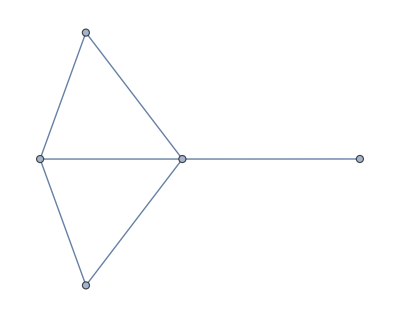

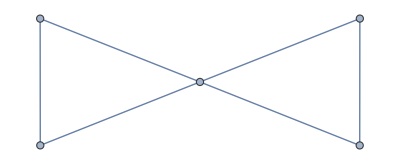

```mathematica
AdjacencyGraph[({{0, 1, 1, 1, 1}, {1, 0, 1, 1, 0}, {1, 1, 0, 0, 0}, {1, 1, 0, 0, 0}, {1, 0, 0, 0, 0}})]
AdjacencyGraph[({{0, 1, 1, 1, 1}, {1, 0, 1, 0, 0}, {1, 1, 0, 0, 0}, {1, 0, 0, 0, 1}, {1, 0, 0, 1, 0}})]
```

```mathematica
inclexcl[gem1,λ,"even"]
inclexcl[gem1,λ,"odd"]
inclexclambdau[gem1,λ,u,"even"]
inclexclambdau[gem1,λ,u,"odd"]
```

(-2+λ)^2 λ (3-3 λ+λ^2)

(-2+λ)^2 (-1+λ)^3

(-2+λ)^2 (-2 u+3 λ+u λ-3 λ^2+λ^3)

(-2+λ)^2 (-1-2 u+3 λ+u λ-3 λ^2+λ^3)

```mathematica
inclexcl[gem2,λ,"even"]
inclexcl[gem2,λ,"odd"]
inclexclambdau[gem2,λ,u,"even"]
inclexclambdau[gem2,λ,u,"odd"]
```

(-2+λ)^2 λ (3-3 λ+λ^2)

(-2+λ)^2 (-1+λ)^3

(-2+λ)^2 (-2 u+3 λ+u λ-3 λ^2+λ^3)

(-2+λ)^2 (-1-2 u+3 λ+u λ-3 λ^2+λ^3)